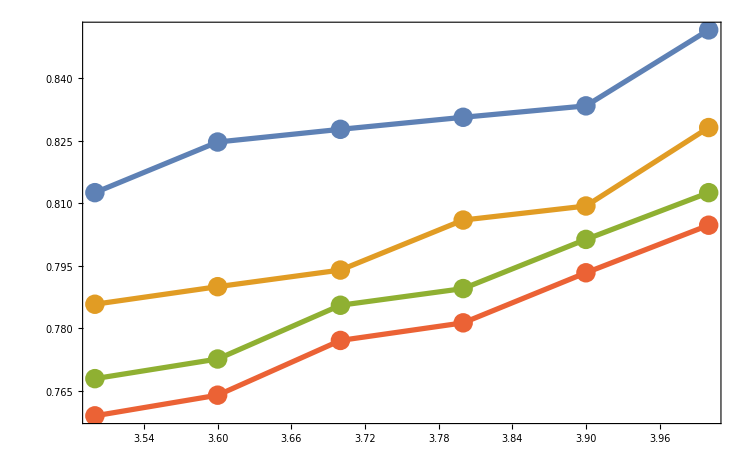

```mathematica
a={{3.5,91/(3.5×32)}, {3.6,95/(3.6×32)},{3.7,98/(3.7×32)},{3.8,101/(3.8×32)}, {3.9,104/(3.9×32)},{4.0,109/(4×32)}};
a2={{3.5,88/(3.5×32)}, {3.6,91/(3.6×32)},{3.7,94/(3.7×32)},{3.8,98/(3.8×32)}, {3.9,101/(3.9×32)},{4.0,106/(4×32)}};
a3={{3.5,86/(3.5×32)}, {3.6,89/(3.6×32)},{3.7,93/(3.7×32)},{3.8,96/(3.8×32)}, {3.9,100/(3.9×32)},{4.0,104/(4×32)}};
a4={{3.5,85/(3.5×32)}, {3.6,88/(3.6×32)},{3.7,92/(3.7×32)},{3.8,95/(3.8×32)}, {3.9,99/(3.9×32)},{4.0,103/(4×32)}};
ListPlot[{a,a2,a3,a4},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True},LabelStyle->Directive[Black,36]]
```

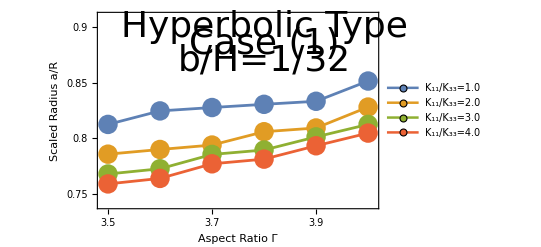

```mathematica
ListPlot[{a,a2,a3,a4},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.75,0.80,0.85,0.9},None},{{3.5,3.6,3.7,3.8,3.9,4},None}}, PlotRange->{{3.49,4.01},{0.74,0.91}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=1.0","K_11/K_33=2.0","K_11/K_33=3.0","K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Left, Top}],Epilog->{Text[Style["Hyperbolic Type",Directive[Black,36]],{3.8,0.9}],Text[Style["Case (1)",Directive[Black,36]],{3.8,0.885}],Text[Style["b/H=1/32",Directive[Black,36]],{3.8,0.87}]}]
```